# Lab 8: Semiconductor Detectors

J.R. Powers-Luhn
jpowersl@vols.utk.edu
Station 1
Partner: Tanner Jacobi

## Using the MCA

1. For each conversion gain, calculate the voltage width per channel.

```mathematica
conversionGains=Table[2^n,{n,8,14}]
```

{256,512,1024,2048,4096,8192,16384}

According to the spec sheet for the Ortex ASPEC-927 MCA (http://www.ortec-online.com/products/electronics/multichannel-analyzers-mca/basic-analog/aspec-927), the voltage range for our MCA is 0-10V.

```mathematica
voltageWidthPerChannel=10/conversionGains//N
```

{0.0390625,0.0195313,0.00976563,0.00488281,0.00244141,0.0012207,0.000610352}

The voltage per channel for the various settings of the Conversion Gain parameter are in the table below:

```mathematica
TableForm[Multicolumn[Join[conversionGains, voltageWidthPerChannel],2]//First, TableHeadings->{None,{"Conversion Gain","Voltage width per Channel"}}]
```

Conversion Gain | Voltage width per Channel
256 | 0.0390625
512 | 0.0195313
1024 | 0.00976563
2048 | 0.00488281
4096 | 0.00244141
8192 | 0.0012207
16384 | 0.000610352

2. Using the conversions from 1, determine the voltage measured by the MCA for the determined channel peak number for each of the four conversion gains.

```mathematica
peaks={324, 2430, 648, 1298};
conversionGains={512, 4096, 1024, 2048};
voltPeaks=peaks*10/conversionGains//N
```

{6.32813,5.93262,6.32813,6.33789}

```mathematica
Mean[voltPeaks]
Mean[{voltPeaks[[1]],voltPeaks[[3]],voltPeaks[[4]]}]
StandardDeviation[voltPeaks]
(Mean[voltPeaks]-voltPeaks[[2]])/StandardDeviation[voltPeaks]
```

6.23169

6.33138

0.199435

1.4996

The peak channel on the MCA software corresponded to a voltage of 6.23V, or 6.33V if the outlier (conversion gain of 4096, approximately 1.5σ below the mean value) is excluded. Error analysis was not conducted as no uncertainty in the 10V max was provided by the MCA manufacturer and the error in the number of bits in the address space was assumed to be zero.

It is assumed that, as the 4096 channel data were collected first while the other settings were collected in rapid

3. From the data recorded, make a properly formatted table of the data (conversion gain, peak channel number, and voltage corresponding to the channel peak number).

```mathematica
TableForm[Multicolumn[Join[conversionGains,peaks,voltPeaks],3]//First,TableHeadings->{None,{"Conversion Gain", "Peak Channel", "Peak Voltage"}}]
```

Conversion Gain | Peak Channel | Peak Voltage
512 | 324 | 6.32813
4096 | 2430 | 5.93262
1024 | 648 | 6.32813
2048 | 1298 | 6.33789

4. From the data in the table and in a text-style cell, discuss the trends seen in the peak channel number and corresponding voltage to the peak channel number. Which one is constant and which one changes? Why does that one change? Does it make sense?

As expected, the peak channel changes while the peak voltage remains constant. Altering the number of channels (bits in the address space) only changes the “binning” when processing the incoming signals. Therefore the size of the voltage range represented by each channel changes, but the input voltage range remains from 0-10V.

MCA Linearity

1. From the spectrum saved (should contain a total of 15 peaks), find the peak channel number (i.e., the average channel number used in a Gaussian fit) for each of the 15 peak regions.
	a. Note: This can be found by multiplying

```mathematica
filedatadata[filename_]:=ToExpression[StringSplit[Import[datafolder<>filename],"\n"][[13;;-17]]]
```

```mathematica
plotfile[filename_]:=ListPlot[filedatadata[filename]];
```

```mathematica
datafolder = NotebookDirectory[]<>"data/czt/";
datafile="Cd_109_CZT_Mar_28_240second.Spe";
```

```mathematica
data=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-17]]];
```

```mathematica
Length[data]
```

8192

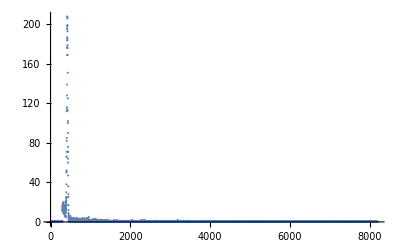

```mathematica
plotfile["Cd_109_CZT_Mar_28_240second.Spe"]
```